#### Uhin Funtzio Totala (erradiala eta angeluarra)

```mathematica
Unprotect[R];
Clear[R];
R[n_,ℓ_][r_]:=(2Z/ (n a))^(3/2) Φ[n,ℓ][r/a]
Unprotect[a,Z];

Unprotect[Φ];
Clear[Φ]; 
Φ[n_Integer,ℓ_Integer][ρ_]:=Module[{const},
const=Sqrt[((n-ℓ-1)!)/((n+ℓ)! 2 n)];
const (2 Z ρ/n)^ℓ  LaguerreL[n-ℓ-1,2 ℓ+1,(2 Z ρ)/n] Exp[-(Z ρ)/n]]
Protect[Φ];

Unprotect[R];
Clear[R];
R[n_,ℓ_][r_]:=(2Z/ (n a))^(3/2) Φ[n,ℓ][r/a]
Unprotect[a,Z];

(*  Subscript[np, x](r, θ,ϕ) = 1/(√2){Subscript[Y, 1]^-1(θ,ϕ)-Subscript[Y, 1]^1(θ,ϕ)} Subscript[R, n, 1](r)  *)
 (* Subscript[np, x] zatia berdina da n guztientzat: *)

a=.5292;
Z=1;
```

```mathematica
convCarts={ r->Sqrt[x^2+y^2+z^2]};
convCartp={Cos[θ]->z/r,Sin[θ]->Sqrt[x^2+y^2]/r, Cos[ϕ]->x/Sqrt[x^2+y^2], Sin[ϕ]->y/Sqrt[x^2+y^2] };
```

#### nd_(z^2) (θ,ϕ) = R_(n, 2)(r) Y_2^0(θ, ϕ)

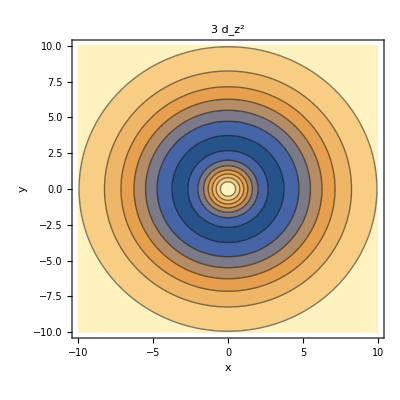

```mathematica
Unprotect[dz2Ang];
Clear[dz2Ang]
dz2Ang[θ_,ϕ_]:= SphericalHarmonicY[2,0,θ,ϕ] 
Protect[dz2Ang];

Unprotect[dz2];
Clear[dz2 ]
 dz2 [r_,θ_,ϕ_][n_]:= 
 SphericalHarmonicY[2, 0,θ,ϕ] *R[n,2][r]
Protect[dz2];

ContourPlot[Evaluate[ dz2[r,θ,ϕ][3]/.convCartp/.convCarts/.z->0],{x,-10,10},{y,-10,10},
PlotPoints->50, PlotRange->All, FrameLabel->{"x","y"},PlotLabel->3"d_(z^2)"]
```

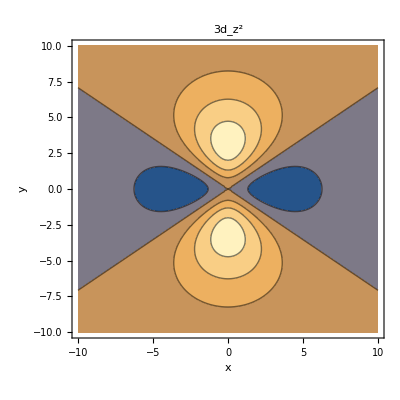

```mathematica
ContourPlot[Evaluate[ dz2[r,θ,ϕ][3]/.convCartp/.convCarts/.y->0,{x,-10,10},{z,-10,10},
PlotPoints->50, PlotRange->All, FrameLabel->{"x","y"},PlotLabel->"3d_(z^2)"]]
```

```mathematica
(* Manipulate[ContourPlot3D[{Evaluate[ dz2[r,θ,ϕ][nn]==0.08/nn/.convCartp/.convCarts],Evaluate[ dz2[r,θ,ϕ][nn]==-0.08/nn/.convCartp/.convCarts]},{x,-50,50},{y,-50,50},{z,-50,50},Contours->10,
PlotPoints->20, PlotRange->All, PlotLabel->nn"d_(z^2)"],{nn,3,7,1},ControlType->PopupMenu] *)
```